```mathematica
h=1/10;
V1[x_]:=x^2 - 0.5*x^4

V[x_]:=4*(Exp[-2*x]-2*Exp[-x])
ℒ=-h^2*u''[x]+V[x]*u[x];
```

```mathematica
{vals,funs}=NDEigensystem[ℒ,u[x],{x,-2,6},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.0079645,-0.0262089,0.0600018,-0.0627409,-0.122501,0.122798,0.193907,-0.202499,0.272266,-0.302499,0.357217,-0.422499,0.448298,0.545161,-0.562499,0.647531,-0.722499,0.755188,0.867946,-0.902499,0.98565,-1.1025,1.10816,1.23537,-1.3225,1.36717,1.50346,-1.5625,1.64418,1.78923,-1.8225,1.93856,2.0921,-2.1025,2.2498,-2.4025,2.4116,2.57746,-2.7225,2.74733,2.92117,-3.0625,3.09894,3.2806,-3.4225,3.46613,3.65547,-3.8025,3.84862,4.04553}

```mathematica
Sort[vals]
```

{-3.8025,-3.4225,-3.0625,-2.7225,-2.4025,-2.1025,-1.8225,-1.5625,-1.3225,-1.1025,-0.902499,-0.722499,-0.562499,-0.422499,-0.302499,-0.202499,-0.122501,-0.0627409,-0.0262089,0.0079645,0.0600018,0.122798,0.193907,0.272266,0.357217,0.448298,0.545161,0.647531,0.755188,0.867946,0.98565,1.10816,1.23537,1.36717,1.50346,1.64418,1.78923,1.93856,2.0921,2.2498,2.4116,2.57746,2.74733,2.92117,3.09894,3.2806,3.46613,3.65547,3.84862,4.04553}

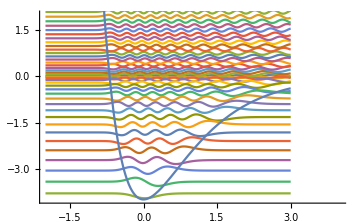

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,-3,3}],Plot[V[x],{x,-3,3}],PlotRange->{{-2,4},{-4,2}},AxesOrigin->{-3,0},ImageSize->Medium]
```

```mathematica
eps_morse=Table[-(2-n-1/2)^2,{n,0,10}]//N
```

{-2.25,-0.25,-0.25,-2.25,-6.25,-12.25,-20.25,-30.25,-42.25,-56.25,-72.25}

```mathematica
eps_qho=Table[h*2*(n+1/2),{n,0,10}]//N
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1}

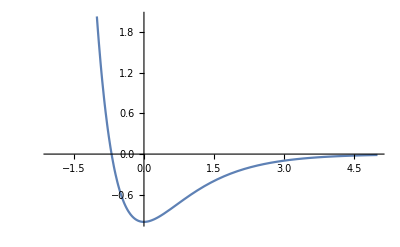

```mathematica
Plot[V[x],{x,-2,5}]
```